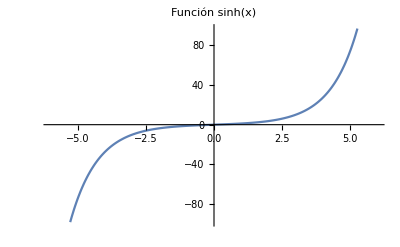

```mathematica
Plot[Sinh[x],{x,-6,6},PlotLabel->"Función sinh(x)"]
```

```mathematica
Plot3D[Exp[x y],{x,-3, 3},{y,-2,2}, PlotLabel->"Función e^(x y)",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[-4 Exp[x y] Sinh[x],{x,-3, 3},{y,-5,5}, PlotLabel->"Discriminante de la EDP", AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Exp[x y]/.{x->0, y->0}
```

1

```mathematica
Plot3D[4 x^2 + 4 x y, {x, -5, 5}, {y, -5, 5}, PlotLabel->"Gráfica del discriminante de la EDP", AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[4 x^2 - 4 x y, {x, -5,5}, {y, -5, 5}, PlotLabel->"Gráfica del discriminante de la EDP", AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
4 x^2 - 4 x y /. {x->-5, y->0}
```

100

```mathematica
m =  Table[{x, y,4 x^2 - 4 x y},{x,-5, 5},{y,-5,5}];
m  // Flatten[#,1]&//Grid
```

-5 | -5 | 0
-5 | -4 | 20
-5 | -3 | 40
-5 | -2 | 60
-5 | -1 | 80
-5 | 0 | 100
-5 | 1 | 120
-5 | 2 | 140
-5 | 3 | 160
-5 | 4 | 180
-5 | 5 | 200
-4 | -5 | -16
-4 | -4 | 0
-4 | -3 | 16
-4 | -2 | 32
-4 | -1 | 48
-4 | 0 | 64
-4 | 1 | 80
-4 | 2 | 96
-4 | 3 | 112
-4 | 4 | 128
-4 | 5 | 144
-3 | -5 | -24
-3 | -4 | -12
-3 | -3 | 0
-3 | -2 | 12
-3 | -1 | 24
-3 | 0 | 36
-3 | 1 | 48
-3 | 2 | 60
-3 | 3 | 72
-3 | 4 | 84
-3 | 5 | 96
-2 | -5 | -24
-2 | -4 | -16
-2 | -3 | -8
-2 | -2 | 0
-2 | -1 | 8
-2 | 0 | 16
-2 | 1 | 24
-2 | 2 | 32
-2 | 3 | 40
-2 | 4 | 48
-2 | 5 | 56
-1 | -5 | -16
-1 | -4 | -12
-1 | -3 | -8
-1 | -2 | -4
-1 | -1 | 0
-1 | 0 | 4
-1 | 1 | 8
-1 | 2 | 12
-1 | 3 | 16
-1 | 4 | 20
-1 | 5 | 24
0 | -5 | 0
0 | -4 | 0
0 | -3 | 0
0 | -2 | 0
0 | -1 | 0
0 | 0 | 0
0 | 1 | 0
0 | 2 | 0
0 | 3 | 0
0 | 4 | 0
0 | 5 | 0
1 | -5 | 24
1 | -4 | 20
1 | -3 | 16
1 | -2 | 12
1 | -1 | 8
1 | 0 | 4
1 | 1 | 0
1 | 2 | -4
1 | 3 | -8
1 | 4 | -12
1 | 5 | -16
2 | -5 | 56
2 | -4 | 48
2 | -3 | 40
2 | -2 | 32
2 | -1 | 24
2 | 0 | 16
2 | 1 | 8
2 | 2 | 0
2 | 3 | -8
2 | 4 | -16
2 | 5 | -24
3 | -5 | 96
3 | -4 | 84
3 | -3 | 72
3 | -2 | 60
3 | -1 | 48
3 | 0 | 36
3 | 1 | 24
3 | 2 | 12
3 | 3 | 0
3 | 4 | -12
3 | 5 | -24
4 | -5 | 144
4 | -4 | 128
4 | -3 | 112
4 | -2 | 96
4 | -1 | 80
4 | 0 | 64
4 | 1 | 48
4 | 2 | 32
4 | 3 | 16
4 | 4 | 0
4 | 5 | -16
5 | -5 | 200
5 | -4 | 180
5 | -3 | 160
5 | -2 | 140
5 | -1 | 120
5 | 0 | 100
5 | 1 | 80
5 | 2 | 60
5 | 3 | 40
5 | 4 | 20
5 | 5 | 0

```mathematica
Plot3D[- 4 x y, {x, -10,10}, {y, -10, 10}, PlotLabel->"Gráfica del discriminante de la EDP", AxesLabel->Automatic]
```

-Graphics3D-

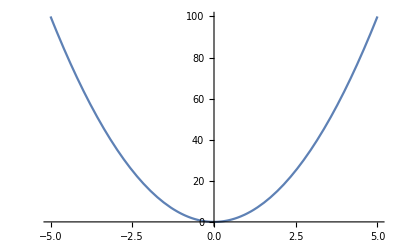

```mathematica
Plot[4x^2,{x,-5,5}]
```